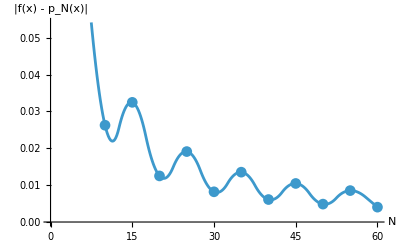

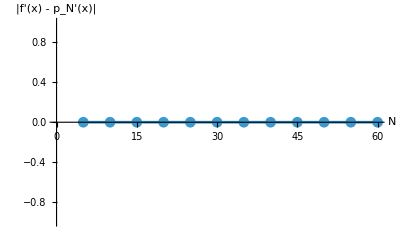

```mathematica
fce[x_]:=Abs[x]

uzly=Range[5,60,5];

pointsChebyshev[nPoints_]:=Sort[Table[N[Cos[j*π/(nPoints-1)]],{j,0,nPoints-1}]];

normDifference1[nPoints_]:=Module[{points1,values1,interp1,tGrid1,error1},
points1=pointsChebyshev[nPoints];
values1=fce/@points1;
interp1=Interpolation[Transpose[{points1,values1}],InterpolationOrder->nPoints-1];
tGrid1=Subdivide[-1,1,nPoints-1];
error1=Max[Abs[fce/@tGrid1-interp1/@tGrid1]];
error1];

normDifference2[nPoints_]:=Module[{points2,values2,interp2,tGrid2,error2},
points2=pointsChebyshev[nPoints];
values2=fce/@points2;
interp2=Interpolation[Transpose[{points2,values2}],InterpolationOrder->nPoints-1];
tGrid2=Subdivide[-1,1,nPoints-1];
error2=Max[Abs[D[fce,x]/@tGrid2-D[interp2,x]/@tGrid2]];
error2];

errors1=Table[{n,normDifference1[n]},{n,uzly}];
ListLinePlot[errors1,AxesLabel->{"N","|f(x) - p_N(x)|"},PlotMarkers->Automatic,InterpolationOrder->2]
errors2=Table[{n,normDifference2[n]},{n,uzly}];
ListLinePlot[errors2,AxesLabel->{"N","|f'(x) - p_N'(x)|"},PlotMarkers->Automatic,InterpolationOrder->2]
```